## Model M/M/1

1. Pracownik otrzymuje zadania do wykonania zgodnie z procesem Poissona ze średnią 5 zadań w ciągu dnia roboczego (8h). Na pojedyncze zadanie przeznacza średnio 45 min, a czas jego wykonania jest zmienną losową o rozkładzie wykładniczym.
-Graphics-
(a) Przez jaką część dnia pracownik jest zajęty?
p0 = 1 - ro = 1/6 pn = (1-ro)* ro^n
(b) Jaka powinna być intensywność napływania zadań, aby pracownik miał średnio nie więcej niż pół godziny wolnego w ciągu dnia?

(c) Ile średnio zadań czeka na realizację?
-Graphics-
(d) Jaki jest średni czas od momentu przekazania zadania do zakończenia jego realizacji?
Wzory Little’a
-Graphics-
(e^*) Przeanalizuj wpływ parametrów strumienia wejściowego i obsługi na wartości charakterystyk stacjonarnych (średni czas przebywania i oczekiwania, średnia długość kolejki, średnia liczba zgłoszeń w systemie, średni czas trwania okresu zajętości, rozkład liczby zgłoszeń dla kilku n).

## Model M/M/1 ze zmiennymi parametrami obsługi

2. Zgłoszenia tworzą strumień Poissona z parametrem λ. Obsługa zajmuje czas wykładniczy z parametrem μ. Jeśli liczba zgłoszeń w systemie spadnie poniżej pewnego poziomu M, szybkość obsługi zostaje zmniejszona do wartości μ_M < μ. Z kolei, jeśli liczba zgłoszeń przekroczy H, szybkość obsługi jest zwiększana do μ_H > μ.
-Graphics-
-Graphics-
(a) Jaki jest warunek stabilności modelu?
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
(b) Zakładając istnienie stanu stacjonarnego, wyznacz rozkład liczby zgłoszeń w systemie.
(c) Wyznacz średnią liczbę zgłoszeń w stanie stacjonarnym.
(d^*) Przeanalizuj wpływ parametrów na charakterystyki stacjonarne

```mathematica
(* a) Przyjmijmy M=5, H=10 *)

M = 5;
H = 10;
suma = p0(1+Sum[ρM^k, {k, 1, M-1}] + Sum[ρM ^(M-1)ρ^(k-M+1), {k, M, H}] + Sum[ρM ^ (M-1)ρ^(H-M+1)ρH^(k-H), {k, H+1, ∞}])
```

p0 (1+ρM+ρM^2+ρM^3+ρM^4+ρ ρM^4+ρ^2 ρM^4+ρ^3 ρM^4+ρ^4 ρM^4+ρ^5 ρM^4+ρ^6 ρM^4-(ρ^6 ρH ρM^4)/(-1+ρH))

```mathematica
rozw = Solve[suma==1, p0] // Flatten
```

{p0→1/(1+ρM+ρM^2+ρM^3+ρM^4+ρ ρM^4+ρ^2 ρM^4+ρ^3 ρM^4+ρ^4 ρM^4+ρ^5 ρM^4+ρ^6 ρM^4-(ρ^6 ρH ρM^4)/(-1+ρH))}

```mathematica
p[k_]=Piecewise[{{ρM^k p0, k<M}, {ρM^(M-1)ρ^(k-M+1)p0, k ≤H}, {ρM^(M-1)ρ^(H-M+1)ρH^(k-H)p0, k ≤H}}] /.rozw
```

Piecewise[{{ρM^k/(1+ρM+ρM^2+ρM^3+ρM^4+ρ ρM^4+ρ^2 ρM^4+ρ^3 ρM^4+ρ^4 ρM^4+ρ^5 ρM^4+ρ^6 ρM^4-(ρ^6 ρH ρM^4)/(-1+ρH)), k<5}, {(ρ^(-4+k) ρM^4)/(1+ρM+ρM^2+ρM^3+ρM^4+ρ ρM^4+ρ^2 ρM^4+ρ^3 ρM^4+ρ^4 ρM^4+ρ^5 ρM^4+ρ^6 ρM^4-(ρ^6 ρH ρM^4)/(-1+ρH)), k≤10}, {0, True}}]

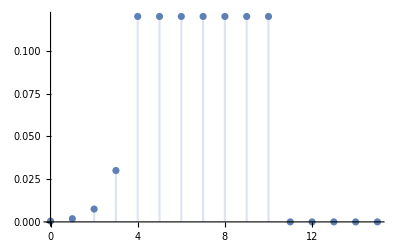

```mathematica
DiscretePlot[p[k]/.{ρM->4,ρ->1,ρH->0.5}, {k,0,15}]
```

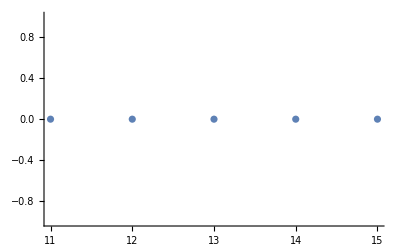

```mathematica
Sum[i p[i], {i, 0, ∞}]/.{ρM->4,ρ->1,ρH->0.5}
```

5.98781

## Model M/M/1 z uciekającymi klientami

3. Samochody pojawiają się na stacji z jednym stanowiskiem obsługi zgodnie z procesem Poissona ze średnią 20/h. Kierowca rezygnuje z tankowania z prawdopodobieństwem q_n=n/4 dla n=1,...,4, gdzie n to liczba samochodów obecnych na stacji. Dla każdego klienta czas obsługi jest zmienną losową o rozkładzie wykładniczym ze średnią 3 min.
-Graphics-
-Graphics-
(a) Znajdź stacjonarny rozkład liczby samochodów na stacji
(b) Wyznacz średni czas przebywania samochodów na stacji w stanie stacjonarnym (uwzględniając wszystkie samochody)
(c) Wyznacz średni czas przebywania na stacji kierowców, którzy zdecydowali się na tankowanie.
(d^*) Niech q_n = n/k dla n = 1, ..., k. Przeanalizuj wpływ wartości parametru k na rozkład i na średnią liczbę samochodów na stacji dla kilku wartości ρ (czy wymagamy, aby ρ < 1?).

```mathematica
p[k_]=4!/(4-k)!(ρ/4)^k p0
```

(3 2^(3-2 k) p0 ρ^k)/((4-k)!)

```mathematica
rozw = Solve[Sum[p[k], {k, 0, 4}] ==1, p0]
```

{{p0→32/(32+32 ρ+24 ρ^2+12 ρ^3+3 ρ^4)}}

```mathematica
p[k_]=p[k]/.rozw
```

{(3 2^(8-2 k) ρ^k)/((32+32 ρ+24 ρ^2+12 ρ^3+3 ρ^4) (4-k)!)}

```mathematica
p[0]
```

{32/(32+32 ρ+24 ρ^2+12 ρ^3+3 ρ^4)}

```mathematica
p[4]
```

{(3 ρ^4)/(32+32 ρ+24 ρ^2+12 ρ^3+3 ρ^4)}

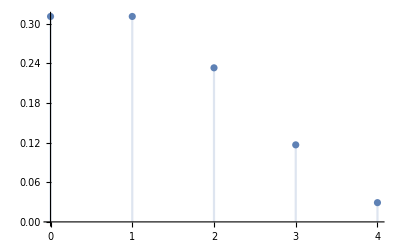

```mathematica
DiscretePlot[p[k]/.ρ->1, {k, 0,4}]
```

```mathematica
EL=Sum[k p[k], {k,0,4}]/.ρ->1
```

{128/103}

```mathematica
(* ze wzoru Littlea*)
```

```mathematica
ES = EL/(1/3)//N
```

{3.72816}

```mathematica
(* W (c) możemy wykrozystać wzór Little'a, ale musimy użyć Lambda**)
```

## Model z grupami klientów

4. Zgłoszenia napływają do serwera zgodnie z procesem Poissona z parametrem λ. Każde z nich składa się z N niezależnych zadań do wykonania, a każde zadanie wymaga czasu wykładniczego ze średnią 1/μ na wykonanie. Liczba zadań wchodzących w skład pojedynczego zgłoszenia ma rozkład P (N = k) = (1 - p) p^(k-1),  k = 1, 2, ..., gdzie p∈[0,1).
(a) Wyznacz rozkład czasu potrzebnego na realizację dowolnego zgłoszenia. 
	Wskazówka: Gdyby liczba zadań przypadająca na zgłoszenie była stała, to czas obsługi miałby pewien rozkład (jaki?), w którym jeden z parametrów odzwierciedla tę liczbę. Tutaj ten parametr jest zmienną losową o pewnym rozkładzie (jakim?). W takiej sytuacji możemy albo wyprowadzić ten rozkład ręcznie (zachęcam do spróbowania, w razie problemów służę pomocą) albo (jako, że są to laboratoria) pójść na łatwiznę i zmusić Mathematicę do zrobienia tego za nas :)  Funkcja ParameterMixtureDistribution[rozklad[parametr], parametr\[Distributed]inny rozklad] wyznaczy rozkład zmiennej losowej o pewnym rozkładzie, gdzie parametr tego rozkładu jest również zmienną losową. W przypadku tego zadania polecam wyznaczyć gęstość (PDF) rozkładu czasu obsługi (wyznaczenie dystrybuanty sprawia Mathematice pewne trudności, co można ominąć wyznaczając po prostu całkę z gęstości) i na tej podstawie ocenić z jakim rozkładem mamy do czynienia. Jak już przez to przebrniecie, pozostałe punkty to będzie łatwizna :)
(b) Znajdź stacjonarny rozkład liczby zgłoszeń w systemie
(c) Przeanalizuj wpływ wartości p na podstawowe stacjonarne charakterystyki modelu dla trzech różnych obciążeń ρ